### Pure Kinetics with Turbine

```mathematica
x={a1,b,bb,c,cc,a2};
M={
{-kon-kkon,+koff,+kkoff,0,0,0},
{+kon,-koff-Kp,0,+Km,0,0},
{+kkon,0,-kkoff-Km,0,+Kp,0},
{0,+Kp,0,-koff-Km,0,+kon},
{0,0,Km,0,-kkoff-Kp,+kkon},
{0,0,0,koff,kkoff,-kon-kkon}
};
M//MatrixForm
```

(-kkon-kon | koff | kkoff | 0 | 0 | 0
kon | -koff-Kp | 0 | Km | 0 | 0
kkon | 0 | -kkoff-Km | 0 | Kp | 0
0 | Kp | 0 | -Km-koff | 0 | kon
0 | 0 | Km | 0 | -kkoff-Kp | kkon
0 | 0 | 0 | koff | kkoff | -kkon-kon)

#### Steady state

```mathematica
(*One of the rows of M is not independent, replace with conservation*)
MSS=Append[M[[;;-2,;;]],{1,1,1,1,1,1}];
MSS//MatrixForm
SS=Solve[MSS.x=={0,0,0,0,0,n},{a1,b,bb,c,cc,a2}]//Simplify;
```

(-kkon-kon | koff | kkoff | 0 | 0 | 0
kon | -koff-Kp | 0 | Km | 0 | 0
kkon | 0 | -kkoff-Km | 0 | Kp | 0
0 | Kp | 0 | -Km-koff | 0 | kon
0 | 0 | Km | 0 | -kkoff-Kp | kkon
1 | 1 | 1 | 1 | 1 | 1)

#### Time scales

```mathematica
λ=Eigenvalues[M]//Simplify;
τ=Abs[1/λ[[2]]];
Λ=DiagonalMatrix[λ];
(*V=Eigenvectors[M]//Simplify;
MUST NORMALISE V
S=V//Transpose;*)
```

#### Work rate in steady state

```mathematica
WdotSS=b(Kp Log[Kp/Km])+c(-Km Log[Kp/Km])+bb(-Km Log[Kp/Km])+cc(Kp Log[Kp/Km])/.SS//Simplify
```

{(2 kkoff kkon koff kon (-Km+Kp) n Log[Kp/Km])/((kkon koff+kkoff (koff+kon)) (kon (kkoff+Km+Kp)+kkon (Km+koff+Kp)))}

#### Work to sort

```mathematica
(*Not in general*)
```

#### Intermediate steady state

```mathematica
IntSS=Solve[M[[2;;-2,;;]].x=={0,0,0,0},{b,bb,c,cc}]//Flatten//Simplify;
(*Assume boxes much larger than channel*)
IntSS=IntSS/.{a2->n-a1}//Simplify
```

{b→(kon (a1 koff+Km n))/(koff (Km+koff+Kp)),bb→(kkon (a1 kkoff+Kp n))/(kkoff (kkoff+Km+Kp)),c→(kon (-a1 koff+(koff+Kp) n))/(koff (Km+koff+Kp)),cc→(kkon (-a1 kkoff+(kkoff+Km) n))/(kkoff (kkoff+Km+Kp))}

#### Evolution of A1 in intermediate SS

```mathematica
a1dotIntSS=M[[1]].x/.IntSS//FullSimplify;
Collect[a1dotIntSS,a1]
(*Evolution is exponential decay to SS*)
a1IntSS=f[t]/.DSolve[f'[t]==(a1dotIntSS/.a1->0)+D[a1dotIntSS,a1]f[t]&&f[0]==n/2,f[t],t];
```

a1 (-kkon-kon+(kkoff kkon)/(kkoff+Km+Kp)+(koff kon)/(Km+koff+Kp))+(kkon Kp n)/(kkoff+Km+Kp)+(Km kon n)/(Km+koff+Kp)

#### Time scale for evolution assuming intermediate steady state

```mathematica
τIntSS=-1/D[a1dotIntSS,a1]//FullSimplify
```

((kkoff+Km+Kp) (Km+koff+Kp))/((Km+Kp) (kon (kkoff+Km+Kp)+kkon (Km+koff+Kp)))

#### Work to sort assuming intermediate SS

```mathematica
(*Work rate as a function of a1 in the intermediate steady state*)
Wdot=b(Kp Log[Kp/Km])+c(-Km Log[Kp/Km])+bb(-Km Log[Kp/Km])+cc(Kp Log[Kp/Km])/.IntSS;
(*Substitute a1(t) expression from above*)
Wdot=Wdot/.a1->a1IntSS//Simplify;
(*Integrate to find total work done in reaching time τ*)
WtotIntSS=Integrate[Wdot,{t,0,τIntSS}]//Simplify;
```

```mathematica
WtotIntSS
```

{-(((Km-Kp) (4 kkon kon (kkoff+Km+Kp) (Km+koff+Kp)+(kon (kkoff+Km+Kp)-kkon (Km+koff+Kp))^2-(kon (kkoff+Km+Kp)-kkon (Km+koff+Kp))^2/ⅇ) n Log[Kp/Km])/(2 (Km+Kp) (kon (kkoff+Km+Kp)+kkon (Km+koff+Kp))^2))}

#### Plots

```mathematica
(*Define entropy*)
S[a1_]:=(a1 Log[a1]+(1-a1)Log[1-a1])/Log[2]
```

Distribution of ΔS

```mathematica
ki=0.001;
kf=0.021;
dk=0.004;
klist=Table[{kon->vkon,koff->vkoff,kkon->vkkon,kkoff->vkkoff,Kp->vKp,Km->vKm},
{vkon,ki,kf,dk},
{vkoff,ki,kf,dk},
{vkkon,ki,kf,dk},
{vkkoff,ki,kf,dk},
{vKm,ki,kf,dk},
{vKp,ki,kf,dk}];
klist=Flatten[klist,5];
(*Eliminate where Kp<Km*)
Position[{Km≤Kp}/.klist//Flatten,_?(#==True&)]//Flatten;
klist=klist[[%]];
klist//Length
```

27216

```mathematica
a1list=(a1/n)/.SS/.klist//Flatten;
Slist=S[a1list];
τlist=τIntSS/.klist;
Wlist=WtotIntSS/n/.klist//Flatten;
```

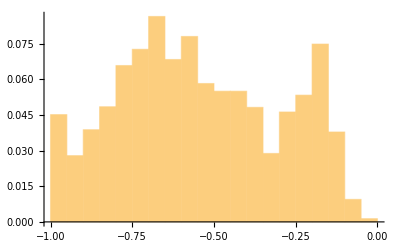

```mathematica
Histogram[Slist,Automatic,"Probability",
PlotRange->{{-1,0},Automatic}]
```

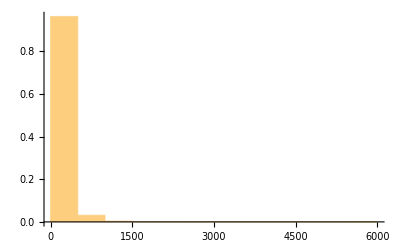

```mathematica
Histogram[τlist,Automatic,"Probability",
PlotRange->Automatic]
```

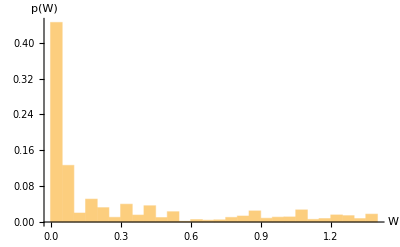

```mathematica
Histogram[Wlist,Automatic,"Probability",
PlotRange->Automatic,
AxesLabel->{Style["W",FontSize->16],Style["p(W)",FontSize->16]}]
```

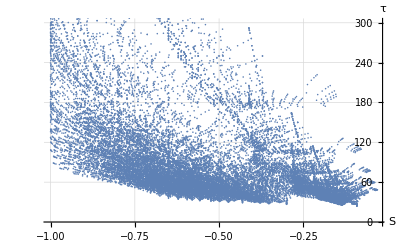

```mathematica
ListPlot[{Slist,τlist}//Transpose,
PlotRange->{All,Automatic},
AxesLabel->{Style["S",FontSize->16],Style["τ",FontSize->16]},
GridLines->Automatic]
```

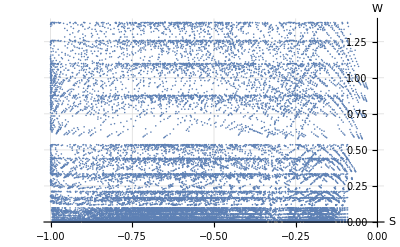

```mathematica
ListPlot[{Slist,Wlist//Flatten}//Transpose,
PlotRange->{{-1,0},Automatic},
AxesLabel->{Style["S",FontSize->16],Style["W",FontSize->16]},
GridLines->Automatic]
```

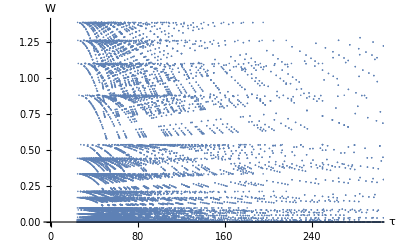

```mathematica
ListPlot[{τlist,Wlist}//Transpose,
PlotRange->Automatic,
AxesLabel->{Style["τ",FontSize->16],Style["W",FontSize->16]}]
```

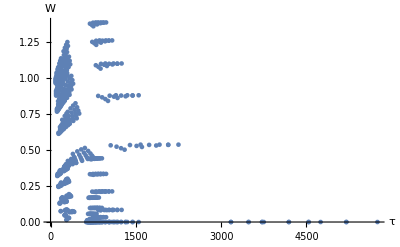
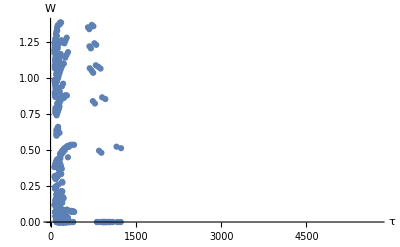
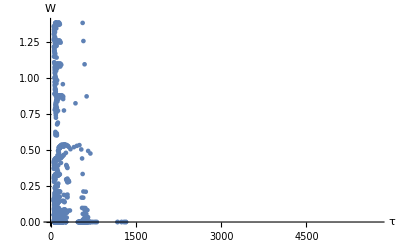
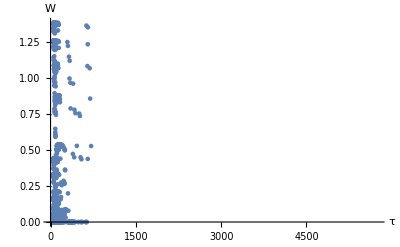
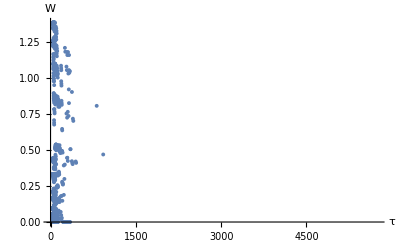
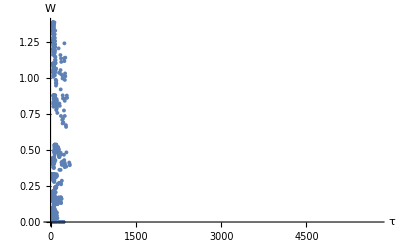
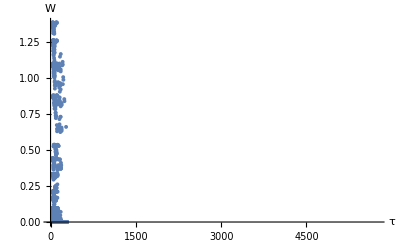
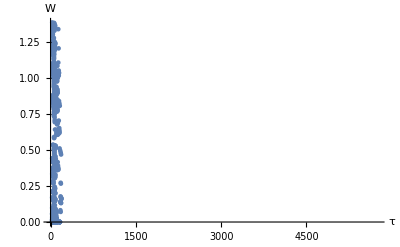
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
dS=0.02;
nchunk=10;
Table[
ListPlot[
{τlist[[Flatten[Position[Slist,_?(Sav-dS≤#≤Sav+dS &)]]]],Wlist[[Flatten[Position[Slist,_?(Sav-dS≤#≤Sav+dS &)]]]]}//Transpose,
PlotRange->{{0,Max[τlist]},{0,Max[Wlist]}},
AxesLabel->{Style["τ",FontSize->16],Style["W",FontSize->16]}
],
{Sav,-1.0,0.0,1/nchunk}]
```